```mathematica
FFT = {{0.052759,146.357815},{0.056098,144.267365},{0.059648,142.270593},{0.063422,140.363264},{0.067436,138.541331},{0.071703,136.800929},{0.076241,135.138365},{0.081065,133.550110},{0.086195,132.032793},{0.091650,130.583191},{0.097449,129.198225},{0.103616,127.874954},{0.110173,126.610563},{0.117145,125.402366},{0.124558,124.247791},{0.132440,123.144381},{0.140821,122.089787},{0.149732,121.081763},{0.159207,120.118158},{0.169282,119.196917},{0.179994,118.316073},{0.191384,117.473743},{0.203495,116.668126},{0.216373,115.897495},{0.230065,115.160198},{0.244624,114.454653},{0.260104,113.779341},{0.276563,113.132808},{0.294064,112.513659},{0.312673,111.920556},{0.332459,111.352212},{0.353497,110.807392},{0.375867,110.284910},{0.399652,109.783624},{0.424942,109.302435},{0.451833,108.840283},{0.480426,108.396149},{0.510827,107.969046},{0.543153,107.558021},{0.577524,107.162155},{0.614070,106.780553},{0.652929,106.412352},{0.694247,106.056709},{0.738179,105.712807},{0.784892,105.379848},{0.834561,105.057055},{0.887372,104.743665},{0.943526,104.438931},{1.003233,104.142121},{1.066718,103.852512},{1.134221,103.569391},{1.205996,103.292053},{1.282312,103.019797},{1.363458,102.751927},{1.449739,102.487749},{1.541479,102.226568},{1.639025,101.967687},{1.742744,101.710404},{1.853026,101.454012},{1.970287,101.197796},{2.094969,100.941027},{2.227540,100.682968},{2.368501,100.422864},{2.518381,100.159942},{2.677746,99.893412},{2.847196,99.622458},{3.027369,99.346241},{3.218944,99.063894},{3.422641,98.774517},{3.639228,98.477180},{3.869522,98.170912},{4.114388,97.854704},{4.374750,97.527502},{4.651588,97.188205},{4.945944,96.835661},{5.258927,96.468660},{5.591716,96.085936},{5.945565,95.686156},{6.321805,95.267918},{6.721854,94.829746},{7.147218,94.370086},{7.599500,93.887297},{8.080403,93.379647},{8.591737,92.845307},{9.135429,92.282344},{9.713526,91.688713},{10.328206,91.062251},{10.981783,90.400666},{11.676720,89.701533},{12.415632,88.962282},{13.201303,88.180189},{14.036692,87.352365},{14.924946,86.475747},{15.869408,85.547087},{16.873637,84.562935},{17.941415,83.519635},{19.076762,82.413301},{20.283955,81.239811},{21.567540,79.994787},{22.932351,78.673580},{24.383529,77.271250},{25.926538,75.782554},{27.567191,74.201919},{29.311665,72.523425},{31.166531,70.740782},{33.138774,68.847306},{35.235823,66.835896},{37.465574,64.699003},{39.836426,62.428607},{42.357307,60.016186},{45.037712,57.452691},{47.887735,54.728547},{50.918109,51.833704},{54.140248,48.757864},{57.566287,45.491118},{61.209128,42.025413},{65.082492,38.357522},{69.200964,34.494170},{73.580057,30.459554},{78.236263,26.304188},{83.187117,22.112174},{88.451265,18.002384},{94.048533,14.119271},{100.000000,10.612137},{106.328081,7.607029},{113.056608,5.180285},{120.210922,3.343690},{127.817966,2.046946},{135.906390,1.195743},{144.506657,0.677482},{153.651155,0.384996},{163.374325,0.231651},{173.712784,0.156332},{184.705470,0.120879},{196.393781,0.104029},{208.821739,0.095151},{222.036148,0.089457},{236.086775,0.084997},{251.026537,0.081052}};
```

```mathematica
CF = {{0.052759,99.949814},{0.056098,99.946638},{0.059648,99.943261},{0.063422,99.939671},{0.067436,99.935853},{0.071703,99.931794},{0.076241,99.927478},{0.081065,99.922888},{0.086195,99.918009},{0.091650,99.912820},{0.097449,99.907303},{0.103616,99.901437},{0.110173,99.895200},{0.117145,99.888569},{0.124558,99.881517},{0.132440,99.874019},{0.140821,99.866047},{0.149732,99.857571},{0.159207,99.848557},{0.169282,99.838974},{0.179994,99.828784},{0.191384,99.817950},{0.203495,99.806429},{0.216373,99.794180},{0.230065,99.781155},{0.244624,99.767307},{0.260104,99.752582},{0.276563,99.736925},{0.294064,99.720277},{0.312673,99.702576},{0.332459,99.683755},{0.353497,99.663743},{0.375867,99.642464},{0.399652,99.619839},{0.424942,99.595782},{0.451833,99.570203},{0.480426,99.543005},{0.510827,99.514086},{0.543153,99.483337},{0.577524,99.450642},{0.614070,99.415878},{0.652929,99.378915},{0.694247,99.339612},{0.738179,99.297822},{0.784892,99.253388},{0.834561,99.206141},{0.887372,99.155905},{0.943526,99.102490},{1.003233,99.045695},{1.066718,98.985306},{1.134221,98.921095},{1.205996,98.852821},{1.282312,98.780227},{1.363458,98.703039},{1.449739,98.620966},{1.541479,98.533700},{1.639025,98.440911},{1.742744,98.342251},{1.853026,98.237347},{1.970287,98.125805},{2.094969,98.007204},{2.227540,97.881098},{2.368501,97.747013},{2.518381,97.604442},{2.677746,97.452849},{2.847196,97.291663},{3.027369,97.120277},{3.218944,96.938046},{3.422641,96.744283},{3.639228,96.538259},{3.869522,96.319197},{4.114388,96.086273},{4.374750,95.838609},{4.651588,95.575273},{4.945944,95.295273},{5.258927,94.997554},{5.591716,94.680995},{5.945565,94.344404},{6.321805,93.986513},{6.721854,93.605975},{7.147218,93.201356},{7.599500,92.771132},{8.080403,92.313683},{8.591737,91.827287},{9.135429,91.310111},{9.713526,90.760208},{10.328206,90.175506},{10.981783,89.553804},{11.676720,88.892761},{12.415632,88.189886},{13.201303,87.442532},{14.036692,86.647885},{14.924946,85.802953},{15.869408,84.904552},{16.873637,83.949300},{17.941415,82.933599},{19.076762,81.853623},{20.283955,80.705305},{21.567540,79.484322},{22.932351,78.186073},{24.383529,76.805670},{25.926538,75.337914},{27.567191,73.777277},{29.311665,72.117882},{31.166531,70.353479},{33.138774,68.477423},{35.235823,66.482649},{37.465574,64.361644},{39.836426,62.106421},{42.357307,59.708490},{45.037712,57.158835},{47.887735,54.447907},{50.918109,51.565685},{54.140248,48.501899},{57.566287,45.246664},{61.209128,41.791953},{65.082492,38.134563},{69.200964,34.281243},{73.580057,30.256208},{78.236263,26.109986},{83.187117,21.926699},{88.451265,17.825250},{94.048533,13.950118},{100.000000,10.450576},{106.328081,7.452749},{113.056608,5.032941},{120.210922,3.202973},{127.817966,1.912546},{135.906390,1.067395},{144.506657,0.554914},{153.651155,0.267939},{163.374325,0.119852},{173.712784,0.049557},{184.705470,0.018905},{196.393781,0.006643},{208.821739,0.002147},{222.036148,0.000638},{236.086775,0.000174},{251.026537,0.000043}};
```

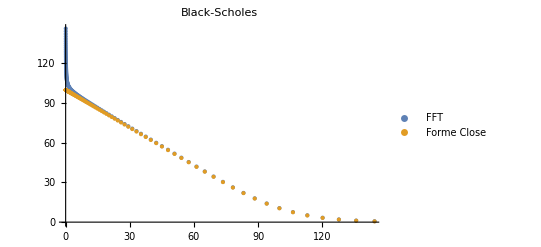

```mathematica
ListPlot[{FFT, CF},PlotLabel->"Black-Scholes", PlotLegends->{"FFT", "Forme Close"},ImageSize->Full]
```

```mathematica
Xx = Table[{FFT[[All,1]][[j]],Abs[1-FFT[[All, 2]][[j]]/CF[[All, 2]][[j]]]},{j,1,Length[FFT[[All, 2]]]}]
```

{{0.052759,0.464313},{0.056098,0.443444},{0.059648,0.423514},{0.063422,0.40448},{0.067436,0.386303},{0.071703,0.368943},{0.076241,0.352364},{0.081065,0.336532},{0.086195,0.321411},{0.09165,0.306971},{0.097449,0.293181},{0.103616,0.280011},{0.110173,0.267434},{0.117145,0.255423},{0.124558,0.243952},{0.13244,0.232997},{0.140821,0.222535},{0.149732,0.212545},{0.159207,0.203003},{0.169282,0.193892},{0.179994,0.18519},{0.191384,0.17688},{0.203495,0.168944},{0.216373,0.161365},{0.230065,0.154128},{0.244624,0.147216},{0.260104,0.140615},{0.276563,0.134312},{0.294064,0.128293},{0.312673,0.122544},{0.332459,0.117055},{0.353497,0.111812},{0.375867,0.106806},{0.399652,0.102026},{0.424942,0.0974605},{0.451833,0.0931009},{0.480426,0.0889379},{0.510827,0.0849624},{0.543153,0.0811662},{0.577524,0.0775411},{0.61407,0.0740795},{0.652929,0.0707739},{0.694247,0.0676175},{0.738179,0.0646035},{0.784892,0.0617254},{0.834561,0.0589773},{0.887372,0.0563533},{0.943526,0.0538477},{1.00323,0.0514553},{1.06672,0.049171},{1.13422,0.0469899},{1.206,0.0449075},{1.28231,0.0429192},{1.36346,0.0410209},{1.44974,0.0392085},{1.54148,0.0374782},{1.63903,0.0358263},{1.74274,0.0342493},{1.85303,0.0327438},{1.97029,0.0313067},{2.09497,0.0299348},{2.22754,0.0286252},{2.3685,0.0273753},{2.51838,0.0261822},{2.67775,0.0250435},{2.8472,0.0239568},{3.02737,0.0229197},{3.21894,0.02193},{3.42264,0.0209856},{3.63923,0.0200845},{3.86952,0.0192248},{4.11439,0.0184046},{4.37475,0.0176223},{4.65159,0.016876},{4.94594,0.0161644},{5.25893,0.0154857},{5.59172,0.0148387},{5.94557,0.0142219},{6.32181,0.0136339},{6.72185,0.0130736},{7.14722,0.0125398},{7.5995,0.0120314},{8.0804,0.0115472},{8.59174,0.0110862},{9.13543,0.0106476},{9.71353,0.0102303},{10.3282,0.00983355},{10.9818,0.00945646},{11.6767,0.00909829},{12.4156,0.00875833},{13.2013,0.00843591},{14.0367,0.00813038},{14.9249,0.00784115},{15.8694,0.00756773},{16.8736,0.00730959},{17.9414,0.00706633},{19.0768,0.00683755},{20.284,0.00662294},{21.5675,0.00642221},{22.9324,0.00623522},{24.3835,0.00606179},{25.9265,0.00590194},{27.5672,0.00575573},{29.3117,0.00562333},{31.1665,0.0055051},{33.1388,0.00540153},{35.2358,0.00531337},{37.4656,0.00524162},{39.8364,0.00518764},{42.3573,0.0051533},{45.0377,0.00514104},{47.8877,0.00515428},{50.9181,0.00519762},{54.1402,0.00527742},{57.5663,0.0054027},{61.2091,0.00558624},{65.0825,0.00584664},{69.201,0.00621118},{73.5801,0.0067208},{78.2363,0.00743784},{83.1871,0.00845887},{88.4513,0.00993725},{94.0485,0.0121256},{100.,0.0154595},{106.328,0.0207011},{113.057,0.0292759},{120.211,0.0439332},{127.818,0.0702728},{135.906,0.120244},{144.507,0.220877},{153.651,0.436879},{163.374,0.932809},{173.713,2.15459},{184.705,5.39402},{196.394,14.6599},{208.822,43.3181},{222.036,139.215},{236.087,487.489},{251.027,1883.93}}

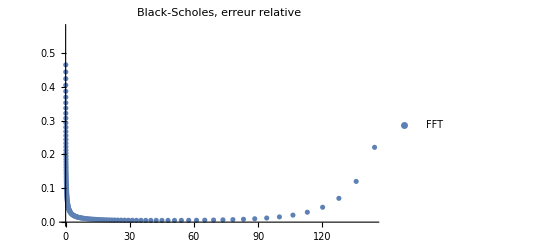

```mathematica
ListPlot[Xx,PlotLabel->"Black-Scholes, erreur relative", PlotLegends->{"FFT", "Forme Close"},ImageSize->Full]
```